```mathematica
gamma={0.01, 0.1};
g=9.8;
F={0.5,1.1,1.7,2.7,3.6};
w=2;
sol=NDSolveValue[{y''[x]+gamma[[1]]y'[x]==-g*Sin[y[x]]+3.5Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
Plot[sol[x],{x,0,60},PlotRange->All]
```

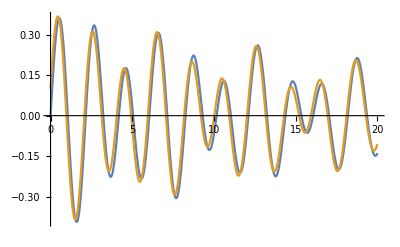

```mathematica
sol1=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[1]]Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol1dx=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[1]]Cos[w*x],y[0]==0.1,y'[0]==1},y,{x,0,100}];
Plot[{Evaluate[y[x]/.sol1/.{C[1]->3}],Evaluate[y[x]/.sol1dx/.{C[1]->3}]},{x,0,20}, PlotRange->All]
```

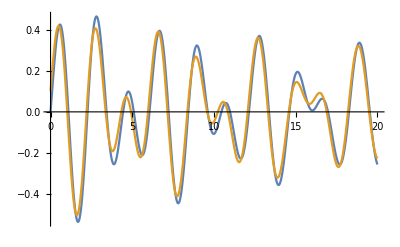

```mathematica
sol2=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[2]]Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol2dx=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[2]]Cos[w*x],y[0]==0.1,y'[0]==1},y,{x,0,100}];
Plot[{Evaluate[y[x]/.sol2/.{C[1]->3}],Evaluate[y[x]/.sol2dx/.{C[1]->3}]},{x,0,20}, PlotRange->All]
```

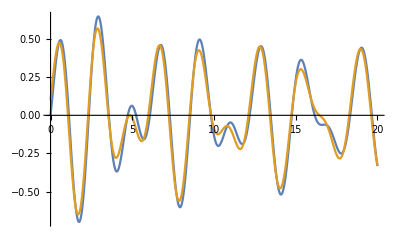

```mathematica
sol3=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[3]]Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol3dx=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[3]]Cos[w*x],y[0]==0.1,y'[0]==1},y,{x,0,100}];
Plot[{Evaluate[y[x]/.sol3/.{C[1]->3}],Evaluate[y[x]/.sol3dx/.{C[1]->3}]},{x,0,20}, PlotRange->All]
```

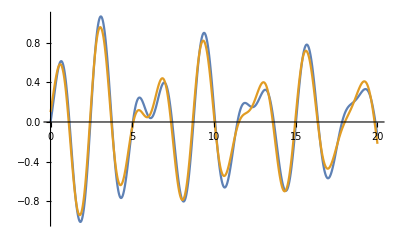

```mathematica
sol4=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[4]]Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol4dx=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[4]]Cos[w*x],y[0]==0.1,y'[0]==1},y,{x,0,100}];
Plot[{Evaluate[y[x]/.sol4/.{C[1]->3}],Evaluate[y[x]/.sol4dx/.{C[1]->3}]},{x,0,20}, PlotRange->All]
```

```mathematica
sol5=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[5]]Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol5dx=NDSolve[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[5]]Cos[w*x],y[0]==0.1,y'[0]==1},y,{x,0,100}];
Plot[{Evaluate[y[x]/.sol5/.{C[1]->3}],Evaluate[y[x]/.sol5dx/.{C[1]->3}]},{x,0,20}, PlotRange->All]
```

```mathematica
Plot[{Evaluate[y[x]/.sol1/.{C[1]->3}],Evaluate[y[x]/.sol2/.{C[1]->3}],Evaluate[y[x]/.sol3/.{C[1]->3}],Evaluate[y[x]/.sol4/.{C[1]->3}],Evaluate[y[x]/.sol5/.{C[1]->3}]},{x,0,20}, PlotRange->All]
```

ReplaceAll::reps: {InterpolatingFunction[{{0.,100.}},{5,7,2,{2631},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{«1»},{0.,1.,3.5,0.0000579484,1.0002,3.49941,0.000115909,1.00041,3.49882,0.000231853,1.00081,3.49765,0.000347843,1.00122,3.49647,0.000463881,1.00162,«18»,3.20066,0.041604,1.12845,3.06858,0.0545652,1.1624,2.93104,0.0679017,1.19476,2.78825,0.0950077,1.25326,2.49455,0.123335,1.30506,«7843»}},{Automatic}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
a=Table[Table[0,400],100];
For[i=1,i<400,i++,
temp=NDSolveValue[{y''[x]+0.1y'[x]==-g*Sin[y[x]]+i/100*Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
For[j=1,j<100,j++;
a[[j,i]]=temp[j];
]
]
MatrixForm[a];
ListPlot[a, PlotRange->All]
res=0;
sol2dx=NDSolveValue[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[5]]Cos[w*x],y[0]==0.01,y'[0]==1},y,{x,0,100}];
sol2=NDSolveValue[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[5]]Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol1=NDSolveValue[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[5]]*Cos[w*x],y[0]==0,y'[0]==1},y,{x,0,100}];
sol1dx=NDSolveValue[{y''[x]+gamma[[2]]y'[x]==-g*Sin[y[x]]+F[[5]]*Cos[w*x],y[0]==0.01,y'[0]==1},y,{x,0,100}];
solve=Table[0,100];

For[i=1,i<100,i++,
solve[[i]]=Log2[Norm[(sol1dx[i]-sol1[i])/(sol1dx[i-1]-sol1[i-1])]];

res=res+Log2[Norm[(sol1dx[i]-sol1[i])/(sol1dx[i-1]-sol1[i-1])]]/99
]

res
```

-0.0198056

-0.0198056